```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/autoindent.wl"];
Autoindent["model/model.wl"];
Autoindent["model/data.wl"];
Autoindent["model/gof-metrics.wl"];
```

```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/model.wl"]
```

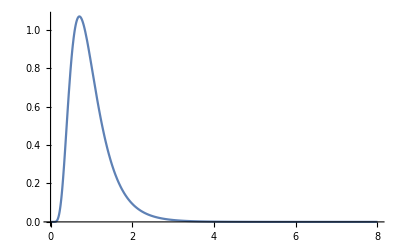

{0.01712,0.0226011,0.0259521,0.0287496,0.0312948,0.0337178,0.0360934,0.0384741,0.0409031,0.0434216,0.0460735,0.0489109,0.0519999,0.0554317,0.0593407,0.0639415,0.0696151,0.0771507,0.0887048,0.120504}

20.

```mathematica
susceptibilityBins=20;
susceptibilityValuesLogNormal[binCount_,stdDev_]:=Module[{m,s,dist,binEdges},
m=-stdDev^2/2;
s=Sqrt[Log[stdDev^2+1]];
dist=LogNormalDistribution[m,s];
Echo[Plot[PDF[dist,x],{x,0,8},PlotRange->All]];
binEdges=InverseCDF[dist,Range[0,binCount]/binCount];
Table[
NIntegrate[x PDF[dist,x],{x,binEdges[[i]],binEdges[[i+1]]}],{i,1,binCount}]//(#/Total[#])&
];
susceptibilityValues=susceptibilityValuesLogNormal[susceptibilityBins,.5]
susceptibilityInitialPopulations=ConstantArray[1/susceptibilityBins,susceptibilityBins];
susceptibilityCoefficient=1./Total[susceptibilityValues*susceptibilityInitialPopulations]
```

Fitting model for CA

>> <|chiSquared→0.0000588118,rmsRelativeError→0.922845,rmsRelativeErrorDeaths→0.88592,rmsRelativeErrorPcr→0.950573,meanRelativeErrorDeaths→0.876142,meanRelativeErrorPcr→0.949391,rSquaredDeaths→1.77505,rSquaredPcr→1.61591,deathResidual7Day→2.5474,pcrResidual7Day→48.1987|>

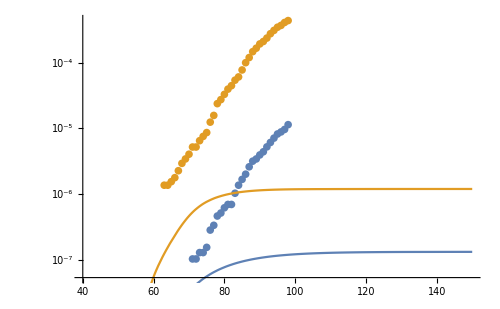
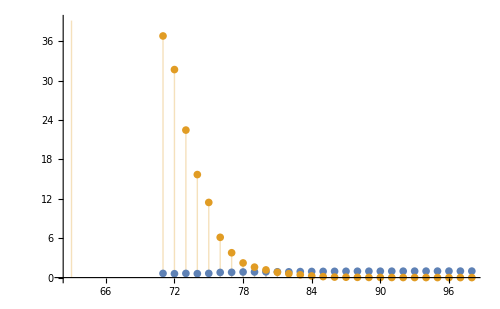
>> Fit for CA
-Graphics--Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 3.70278 | 341.721 | 0.0108357 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[0.0108357,60.,HypothesisTesting`TwoSided→True]
ⅇ^importtime | 53.5702 | 153.649 | 0.348654 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[0.348654,60.,HypothesisTesting`TwoSided→True]
ⅇ^stateAdjustmentForTestingDifferences | 1.95895 | 14.6134 | 0.134052 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[0.134052,60.,HypothesisTesting`TwoSided→True]
ⅇ^distpow | 1.62588 | 7153.93 | 0.000227271 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[0.000227271,60.,HypothesisTesting`TwoSided→True] | DF | SS | MS
Model | 4 | 1.37694×10^-11 | 3.44235×10^-12
Error | 60 | 8.62205×10^-10 | 1.43701×10^-11
Uncorrected Total | 64 | 8.75974×10^-10 | 
Corrected Total | 63 | 8.5923×10^-10 |

>> Current scenario Generating simulations for CA in the

>> Generating simulations for CA in the  Italy scenario

>> Generating simulations for CA in the  Wuhan scenario

>> Generating simulations for CA in the  Normal scenario

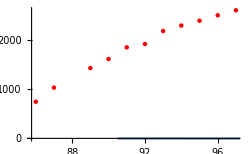
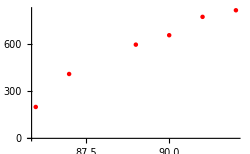
>> Current Hospitalizations for CA
-Graphics-Cumulative Hospitalizations for CA
-Graphics-Current ICU for CA
-Graphics-Cumulative ICU for CA
-Graphics-

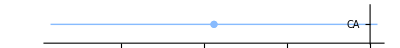
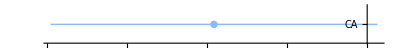
Currently Hospitalized
-Graphics- | Cumulative Hospitalized
-Graphics- | Currently ICU
-Graphics- | Cumulative ICU
-Graphics-

state | distancingLevel | id | distancingDays | maintain | name | totalProjectedDeaths | totalProjectedPCRConfirmed | totalProjectedInfected | totalInfectedFraction | fatalityRate | fatalityRateSymptomatic | fatalityRatePCR | fractionOfInfectionsPCRConfirmed | dateContained | dateICUOverCapacity | dateHospitalsOverCapacity | {"r0natural", "importtime", "stateAdjustmentForTestingDifferences"} |  | 
CA | 81/140 | scenario1 | 90 | True | Current | 5.43494 | 50.4954 | 511.11 | 0.0000131111 | 0.0106336 | 0.0151909 | 0.107632 | 0.141137 | - | - | - | 3.70278 | 53.5702 | 1.95895
CA | 0.4 | scenario2 | 90 | False | Italy | 5.50239 | 47.2164 | 580.744 | 0.0000148974 | 0.00947472 | 0.0135353 | 0.116536 | 0.116147 | - | - | - | 3.70278 | 53.5702 | 1.95895
CA | 0.11 | scenario3 | 60 | False | Wuhan | 2.90649 | 31.7829 | 354.462 | 9.09277×10^-6 | 0.00819972 | 0.0117139 | 0.0914482 | 0.128093 | - | - | - | 3.70278 | 53.5702 | 1.95895
CA | 1 | scenario4 | 90 | False | Normal | 4.97007 | 49.6334 | 501.066 | 0.0000128535 | 0.00991898 | 0.01417 | 0.100136 | 0.141508 | - | - | - | 3.70278 | 53.5702 | 1.95895

```mathematica
asd=GenerateModelExport[10,{"CA"}];
TableForm[Import["tests/summary.csv"]]
```